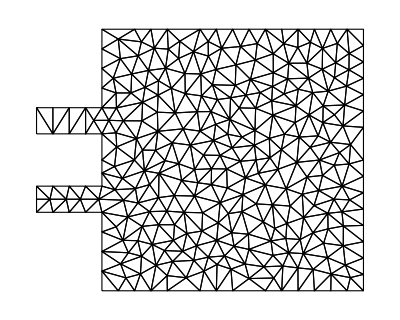

```mathematica
(* Start of given code *)
slits={Rectangle[{-0.25,0.3},{0, 0.4}],Rectangle[{-0.25,0.6},{0, 0.7}]};
square=Rectangle[{0,0},{1,1}];
Ω=RegionUnion[slits⟦1⟧,slits⟦2⟧,square];
Needs["NDSolve`FEM`"]
mesh=ToElementMesh[Ω, "MeshOrder"-> 1];
mesh["Wireframe"]
(*Remove semicolon for more detailed mesh*)
Show[mesh["Wireframe"["MeshElementIDStyle"->Red]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Blue]]];
nodes = mesh["Coordinates"];
elements = mesh["MeshElements"]⟦1,1⟧;
boundary =Flatten[mesh["BoundaryElements"]⟦1,1⟧];
boundary=DeleteDuplicates[boundary];
Subscript[Γ, D]=Cases[nodes⟦boundary⟧,{x_,_}/;x== -0.25];
boundNodes = Flatten[Nearest[nodes->"Index",Subscript[Γ, D],1]];
(* End of given code *)
periodicElems=Table[{Position[nodes,Sort[Subscript[Γ, D]]⟦i⟧]⟦1,1⟧,Position[nodes,Sort[Subscript[Γ, D]]⟦i+1⟧]⟦1,1⟧},{i,1,Length[Subscript[Γ, D]]-1}];
periodicCoords=Table[nodes⟦periodicElems[[k]]⟧,{k,1,Length@periodicElems}];
periodicBoundary=Select[mesh["BoundaryElements"]⟦1,1⟧, MemberQ[ns,nodes⟦#⟧]&];
```

```mathematica
(* Standard basis functions, i.e. shape functions *)
Subscript[ψ, 0][{ξ_,η_}]:=1-ξ-η
Subscript[ψ, 1][{ξ_,η_}]:=ξ
Subscript[ψ, 2][{ξ_,η_}]:=η
gradψ=Transpose@Grad[{Subscript[ψ, 0][{ξ,η}],Subscript[ψ, 1][{ξ,η}],Subscript[ψ, 2][{ξ,η}]},{ξ,η}];
gradψT=Transpose@gradψ;

(* The Jacobian and Jacobian inverse *)
(* Here we utilise the fact that R^2 vectors are represented as lists and we can directly get their "transpose" by using the list *)
J[elementNodes_]:={
elementNodes⟦2⟧-elementNodes⟦1⟧,
elementNodes⟦3⟧-elementNodes⟦1⟧}
B[elementNodes_]:={
{elementNodes⟦3,2⟧-elementNodes⟦1,2⟧,elementNodes⟦1,2⟧-elementNodes⟦2,2⟧},
{elementNodes⟦1,1⟧-elementNodes⟦3,1⟧,elementNodes⟦2,1⟧-elementNodes⟦1,1⟧}}

(* The local stiffness matrix *)
(* Formally, we would have to do something like this 
localStiffness[nodes_, element_]:=
1/(Det@J[nodes,element])NIntegrate[gradψT.(Transpose@B[nodes,element]).B[nodes,element].gradψ,{ξ,0,1},{η,0,1-ξ}]*)
(* However the integrand is constant so we just need to multiply it by the area of the standard triangle, which is 1/2 *)
localStiffness[elementNodes_]:=
0.5/(Det@J[elementNodes])gradψT.Transpose@B[elementNodes].B[elementNodes].gradψ
(* Same comments apply to localMass *)
localMass[elementNodes_]:=0.5Det@J[elementNodes]gradψT.gradψ


FEMMatrix[nodes_,elements_,localFunction_,nullNodes_]:=Module[{
globalMatrix = ConstantArray[0,{Length@nodes,Length@nodes}], element, stiffness},
For[k=1,k≤Length@elements,k++,
element = elements⟦k⟧;
stiffness=localFunction@nodes⟦element⟧;
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
globalMatrix⟦element⟦i⟧,element⟦j⟧⟧+=stiffness⟦i, j⟧;
];
];
];

(* We should now take into account that some of the coefficients will have to be 0 to ensure the boundary condition of u=0 *)
For[i=1,i≤Length@nullNodes,i++,
For[j=1,j≤Length@nodes,j++,
globalMatrix⟦j,nullNodes⟦i⟧⟧=0;
globalMatrix⟦nullNodes⟦i⟧,j⟧=0;
];
globalMatrix⟦nullNodes⟦i⟧,nullNodes⟦i⟧⟧=1;
];

globalMatrix
]

(* The function that assebles the global stiffness matrix *)
stiffnessMatrix[nodes_,elements_,nullNodes_]:=FEMMatrix[nodes,elements,localStiffness,nullNodes]

(* The function that assebles the global mass matrix *)
massMatrix[nodes_,elements_,nullNodes_]:=FEMMatrix[nodes,elements,localMass,nullNodes]



(* The generalised local inner load array *)
generalLocalInnerLoad[f_,elementNodes_]:=Module[
{jacobian = J@elementNodes,
origin=elementNodes⟦1⟧},
1/6 Det[jacobian]Table[
Subscript[ψ, s][{0.5,0}]f[jacobian.{0.5,0}+origin]+
Subscript[ψ, s][{0.5,0.5}]f[jacobian.{0.5,0.5}+origin]+
Subscript[ψ, s][{0,0.5}]f[jacobian.{0,0.5}+origin],{s,0,2}]
]
(* The inner load for this problem *)
localInnerLoad[elementNodes_]:=generalLocalInnerLoad[0&,elementNodes]

(* The local boundary load array *)
localBoundaryLoad[boundaryElementNodes_]:=(
ConstantArray[
0.5Norm[boundaryElementNodes⟦1⟧-boundaryElementNodes⟦2⟧],
2]
)

(* boundaryElements holds only the boundary elements that don't evaluate to 0 *)
loadVector[nodes_,elements_,boundaryElements_,localInnerLoadFunction_,localBoundaryLoadFunction_,nullNodes_]:=Module[{
globalVector=ConstantArray[0,Length@nodes],element},

(* The load from double integrals *)
For[k=1,k≤Length@elements,k++,
element = elements⟦k⟧;
globalVector⟦element⟧+=localInnerLoadFunction[nodes⟦element⟧];
];

(* The load from boundary integrals *)
For[k=1,k≤Length@boundaryElements,k++,
globalVector⟦boundaryElements⟦k⟧⟧+=localBoundaryLoadFunction@nodes⟦boundaryElements⟦k⟧⟧;
];

(* Where u=0 we should have loadVector=0 *)
globalVector⟦nullNodes⟧=0;

globalVector
]

ConcentrateMatrix[M_?MatrixQ]:=DiagonalMatrix[Total/@M]
ApproximateInverse[M_?MatrixQ]:=DiagonalMatrix[1/#&@*Total/@M]
```

```mathematica
(* Obviously b is the zero vector and so we remove it from consideration from now on *)
(* dirichletNodeFunctions is a list of (list of nodes and function) - each set of nodes has its corresponding function to give it values in the recurrence relation *)
solveEquation[nodes_,elements_,dirichletNodeFunctions_,T_,τ_]:=Module[{
n=Length@nodes,timeSteps=Ceiling@(T/τ),
Subscript[M, 0],Subscript[M, 1],A,I,recurrenceMatrix,temp,
dirichletNodes=First/@dirichletNodeFunctions,sol},

Subscript[M, 0]=massMatrix[nodes,elements,dirichletNodes];
Subscript[M, 1]=stiffnessMatrix[nodes,elements,dirichletNodes];
I=IdentityMatrix[n];
temp=-Inverse@Subscript[M, 0].Subscript[M, 1];
A=ConstantArray[0,{n,n}];

(* Fill A *)
For[k=1,k≤n,k++,
(* Fill upper right with identity matrix *)
(*A⟦k,n+k⟧=1;*)
A⟦k⟧=PadLeft[temp⟦k⟧,2n];

(* Fill lower left with temp *)
A⟦n+k⟧=PadRight[temp⟦k⟧,2n];
];
recurrenceMatrix=Inverse[I-τ/2 A].(I+τ/2 A);

sol=ConstantArray[0,{timeSteps, 2n}];
(* We also assume u'(0, x̄) = 0 *)
For[k=2,k≤timeSteps,k++,
sol⟦k+1⟧=recurrenceMatrix.sol⟦k⟧;
(* Take into account the dirichlet conditions *)
For[i=1,i≤Length@dirichletNodeFunctions,i++,
{someNodes, someFunction}=dirichletNodeFunctions⟦i⟧;
sol⟦k+1, someNodes⟧=someFunction[nodes⟦#⟧,kτ]&/@someNodes;
];
(*sol⟦k+1,⟧*)
];

(* Return only the q component of the solution *)
Take[#,n]&/@sol
]
```

```mathematica
boundaryPeriodicFunction[{x_,y_},t_]:=0.1Sin[8Pi t]
q=solveEquation[nodes,elements,{{boundNodes,boundaryPeriodicFunction}},2,0.005];
```